## JIDHUN PP | BSc(Hons) Computer Science| 20211419|Practical-2 Plotting of second order solution family of differential equation Question 1:Solve Second order differential Equation y’’+y=0 Solution:

```mathematica
DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

## Question 2:Solve Second order differential Equation y’’+y’-6y=0 Solution:

```mathematica
DSolve[y''[x]+y'[x]-6y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

## Question 3::Solve Second order differential Equation 4y’’+12y’-6y=0 Solution:

```mathematica
DSolve[4y''[x]+12y'[x]-6y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-3/2-(√15)/2) x) C[1]+ⅇ^((-3/2+(√15)/2) x) C[2]}}

## Question 4:Solve Second order differential Equation y’’-6y’+13y=0 Solution:

```mathematica
DSolve[y''[x]-6y'[x]+13y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[2] Cos[2 x]+ⅇ^(3 x) C[1] Sin[2 x]}}

## Question 5::Solve Second order differential Equation y’’-2y’+y=0 Solution:

```mathematica
DSolve[y''[x]-2y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]}}

## Plotting Of Solution Of Second Order Differential Equation Question1:Solve Second order differential Equation y’’+y=0 and Plot its three solutions: Solution:

```mathematica
Sol=DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2}
```

Cos[x]+2 Sin[x]

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->1/2,C[2]->5}
```

Cos[x]/2+5 Sin[x]

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-4}
```

-Cos[x]-4 Sin[x]

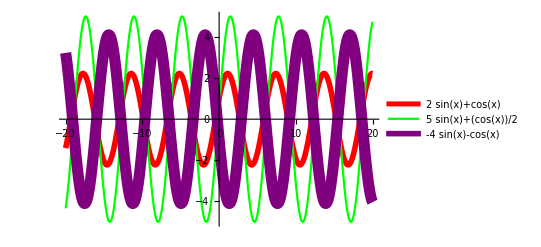

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

## Question 2:Solve Second order differential Equation y’’+y’-6y=0 and Plot its three solutions: Solution:

```mathematica
Sol=DSolve[y''[x]+y'[x]-6y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->0,C[2]->2.5}
```

2.5 ⅇ^(2 x)

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->5}
```

ⅇ^(-3 x)+5 ⅇ^(2 x)

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->5}
```

-1/2 ⅇ^(-3 x)+5 ⅇ^(2 x)

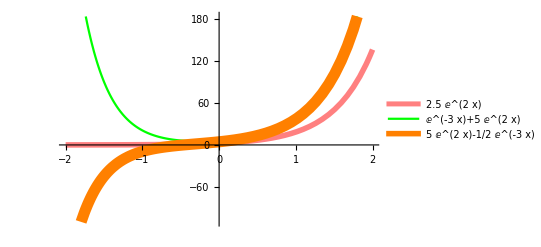

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-2,2},
PlotStyle->{{Pink,Thickness[0.01]},{Green,Thick},{Orange,Thickness[0.02]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

```mathematica
Question 3:Solve Second order differential Equation 4y''+12y'+9y=0 and Plot its four solutions for
(i)C[1]=-1,C[2]=4
(ii)C[1]=-3,C[2]=6
(iii)C[1]=-10,C[2]=7
(iv)C[1]=-1.5C[2]=-5
Solution:
```

```mathematica
Sol=DSolve[4y''[x]+12y'[x]+9y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-3 x/2) C[1]+ⅇ^(-3 x/2) x C[2]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->4}
```

-ⅇ^(-3 x/2)+4 ⅇ^(-3 x/2) x

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->3,C[2]->6}
```

3 ⅇ^(-3 x/2)+6 ⅇ^(-3 x/2) x

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10,C[2]->7}
```

-10 ⅇ^(-3 x/2)+7 ⅇ^(-3 x/2) x

```mathematica
Sol4=y[x]/.Sol[[1]]/.{C[1]->-1.5,C[2]->-5}
```

-1.5 ⅇ^(-3 x/2)-5 ⅇ^(-3 x/2) x

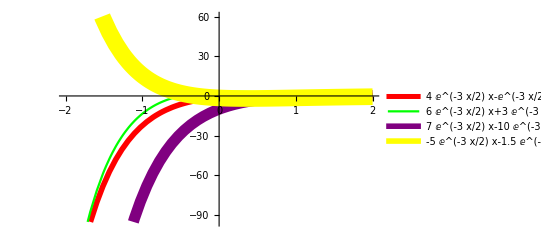

```mathematica
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-2,2},
PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]},{Yellow,Thickness[0.03]}},
PlotLegends->{Sol1,Sol2,Sol3,Sol4}]
```

### Question 4:Solve Second order differential Equation 4y’’-6y’+13y=0 and Plot its any three solutions Solution:

```mathematica
Sol=DSolve[4y''[x]-6y'[x]+13y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(3 x/4) C[2] Cos[(√43 x)/4]+ⅇ^(3 x/4) C[1] Sin[(√43 x)/4]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->4}
```

4 ⅇ^(3 x/4) Cos[(√43 x)/4]-ⅇ^(3 x/4) Sin[(√43 x)/4]

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->3,C[2]->6}
```

6 ⅇ^(3 x/4) Cos[(√43 x)/4]+3 ⅇ^(3 x/4) Sin[(√43 x)/4]

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10,C[2]->7}
```

7 ⅇ^(3 x/4) Cos[(√43 x)/4]-10 ⅇ^(3 x/4) Sin[(√43 x)/4]

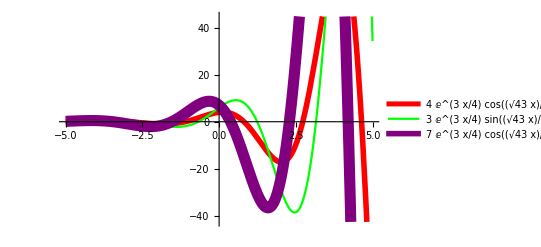

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-5,5},
PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

### Question 5:Solve Second order differential Equation y’’-2y’+y=0 and Plot its any five solutions Solution:

```mathematica
Sol=DSolve[y''[x]-2y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->0.5,C[2]->3}
```

0.5 ⅇ^x+3 ⅇ^x x

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->-3,C[2]->-2}
```

-3 ⅇ^x-2 ⅇ^x x

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->7}
```

-ⅇ^x+7 ⅇ^x x

```mathematica
Sol4=y[x]/.Sol[[1]]/.{C[1]->-6,C[2]->1}
```

-6 ⅇ^x+ⅇ^x x

```mathematica
Sol5=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2/3}
```

ⅇ^x+(2 ⅇ^x x)/3

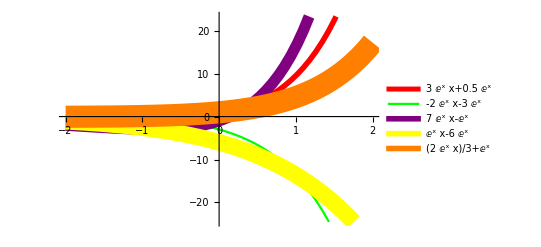

```mathematica
Plot[{Sol1,Sol2,Sol3,Sol4,Sol5},{x,-2,2},
PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]},{Yellow,Thickness[0.03]},{Orange,Thickness[0.04]}},
PlotLegends->{Sol1,Sol2,Sol3,Sol4,Sol5}]
```